```mathematica
(*Standard Bethe ansatz definition t_nm=2 Min(m,n)-\delta_mn *)
t[i_,j_]:=2.Min[i,j]-1.KroneckerDelta[i,j];

(*Upper bound for string Bethe-Takahashi numbers *)
UpB[L_,M_,α_,n_]:=(L-1.-Sum[t[n,j]α[[j]],{j,1.,M}])/2.;

(* Select a Bethe-Takahashi number configuration at random *)
BTsel[M_,L_,α_]:=Block[{J,n,k},
J=Table[RandomSample[Table[k,{k,-UpB[L,M,α,n],
UpB[L,M,α,n]}],α[[n]]],{n,1,M}];J];

(* Scattering phases for the Bethe-Takahashi equations *)
Theta[x_,m_,n_]:=If[n!=m,2ArcTan[x/Abs[n-m]]+
4Sum[ArcTan[x/(Abs[n-m]+k)],{k,2,n+m-Abs[n-m]-2,2}]
+2ArcTan[x/(n+m)],4Sum[ArcTan[x/k],{k,2,2n-2,2}]+
2ArcTan[x/(2n)]];

(* Select the number of down spins M with probability *)
(* (Binomial[L,M]-Binomial[L,M-1])/Binomial[L,L/2] *)
choM[L_]:=Block[{a,p,check},
check=0;
While[check==0,
a=RandomInteger[{0,L/2}];
p=RandomReal[{0,1}];
If[p<=(Binomial[L,a]-Binomial[L,a-1])/(Binomial[L,L/2]),
check=1;];];a];

(* Generate a random string (uniformly distributed) using the *)
(* integer partitions of M *)
GenString[M_]:=Block[{part,part1,pair,d,j,k,m,p,
check},
m=M;
part=Reap[While[m!=0,
d=IntegerPart[RandomReal[{1.,M+1-10^(-12)}]];
j=IntegerPart[RandomReal[{1.,M+1-10^(-12)}]];
p=RandomReal[{0,1}];

If[p<=Re[(d PartitionsP[m-j d])/(m PartitionsP[m])],
Sow[Table[d,{k,1,j}]];
m=m-j d;];];][[2]];

(* Convert the partition to standard string format *)
part1=Flatten[part];
Table[Count[part1,i],{i,1,M}]];

ChooString[M_,L_]:=Block[{string,mat,DDol,DDne,i,j,
strNe,p,vec,vec1},
mat=Table[t[i,j],{i,1,M},{j,1,M}];
check=1;
While[check==1,
strNe=GenString[M];
DDne=Product[Binomial[L-Total[Table[mat[[i,j]]strNe[[j]],
{j,1,M}]],strNe[[i]]],{i,1,M}];
p=RandomReal[{0,1}];
If[p<=Min[1,Re[DDne/(Binomial[L,M]-Binomial[L,M-1])]],string=strNe;check=0;];];
string];
(* Metropolis step to accept a Bethe Takashi quantum numbers *)
(* configuration *)
Metropolis[Mo_,Mn_,Eo_,En_,L_,β_]:=Block[{p},
p=RandomReal[{0.,1.}];

(*PART TO BE MODIFIED TO INCLUDE MORE CHARGES*)
If[p<=Min[1.,Abs[(L-2.Mn+1.)/(L-2.Mo+1.)Exp[-β[[1]](En[[1]]-Eo[[1]])-β[[2]](En[[2]]-Eo[[2]])-β[[3]](En[[3]]-Eo[[3]])-β[[4]](En[[4]]-Eo[[4]])]]],1,0]
];

Metro=Compile[{Mo,Mn,Eo,En,L,β},
Metropolis[Mo,Mn,Eo,En,L,β],CompilationTarget:>"C"];

(* Solve the Bethe-Takahashi equations for a given string *)
(* configuration "string" and Bethe-Takahashi numbers "BN" *)

(*PART TO BE MODIFIED TO INCLUDE MORE CHARGES*)
SolveBethe[M_,L_,string_,BN_]:=Block[{sol,x,n,g,b,m,o,h,check,sol1,bit,EE,EE1,EE2,EE3},
check=1;
bit=0;
sol=Table[x[n][g],{n,1,M},{g,1,string[[n]]}]/.FindRoot[
Flatten[Table[ArcTan[x[n][g]/n]-π BN[[n,g]]/L-1/(2L)
∑_(m=1)^M ∑_(b=1)^string[[m]] If[m!=n||b!=g,Theta[x[n][g]-x[m][b],m,n],
0]==0,{n,1,M},{g,1,string[[n]]}]],Flatten[Table[
{x[o][h],RandomReal[]},{o,1,M},{h,1,string[[o]]}],1],
WorkingPrecision->15,MaxIterations->200,AccuracyGoal->15]//
Quiet;

check=Flatten[Table[ArcTan[sol[[n]][[g]]/n]-π BN[[n,g]]/L-
1/(2L)∑_(m=1)^M ∑_(b=1)^string[[m]] If[m!=n||b!=g,Theta[sol[[n]][[g]]-
sol[[m]][[b]],m,n],0],{n,1,M},{g,1,string[[n]]}]];
If[Total[Abs[check]]>10^-10,Print["Findroot failed with string"];
Print[BN];
bit=1;];
EE=If[M!=0,(*L/4.*)-Total[Flatten[Table[2.n/((sol[[n,g]])^2.+n^2.),
{n,1,M},{g,1,string[[n]]}]]],L/4.];

(*PART TO BE MODIFIED TO INCLUDE MORE CHARGES*)
EE1=-Total[Flatten[Table[4.n*sol[[n,g]]/((sol[[n,g]])^2.+n^2.)^2,
{n,1,M},{g,1,string[[n]]}]]];
EE2=Total[Flatten[Table[2.n*(n^2-3*(sol[[n,g]])^2)/((sol[[n,g]])^2.+n^2.)^3,
{n,1,M},{g,1,string[[n]]}]]];
EE3=Total[Flatten[Table[8.n*sol[[n,g]]*(n^2-(sol[[n,g]])^2)/((sol[[n,g]])^2.+n^2.)^4,
{n,1,M},{g,1,string[[n]]}]]];
Flatten[{bit,EE,EE1,EE2,EE3,Chop[sol]}]
];

(* Inizialization from the ground state sector β is the *)
(* temperature *)
L=12;
Mo=L/2;
MCS=10000;
tsweeps=0;

(*Creutz Demon update*)
EDD={};
(*Initial demon energy*)
DE=6;
CDemon[Eo_,enertemp_,DE_]:=Block[{check,de,DCEmax},
(*maximum amount of energy exchanged by the demon*)
DCEmax=.1;
check=0;
If[Chop[enertemp-Eo]≤ 0,
If[DE+Abs[enertemp-Eo]≤ DCEmax,
de=DE+Abs[Eo-enertemp];
check=1;
];,
If[Abs[enertemp-Eo]≤ DE,
de=DE-Abs[enertemp-Eo];
check=1;
];
];
{check,de}
];

(*PART TO BE MODIFIED TO INCLUDE MORE CHARGES*)
β={SetPrecision[0./1.0,30],SetPrecision[0.,30],SetPrecision[0.,30],SetPrecision[0.,30]};
strNe=ChooString[Mo,L];
BTnum=SetPrecision[BTsel[Mo,L,strNe],30];
sol=SolveBethe[Mo,L,strNe,BTnum];
(*PART TO BE MODIFIED TO INCLUDE MORE CHARGES*)
Eo={sol[[2]],sol[[3]],sol[[4]],sol[[5]]};
(*Select energy density 1/2*)
DE=(*DE-Abs[Eo[[1]]];*)0;
Print[Eo[[1]]];
Print[DE];

(* Metropolis update *)
BNumberst=BTnum;
Strconf=strNe;
Rap=sol;
i=1;

(*PART TO BE MODIFIED TO INCLUDE MORE CHARGES*)
Monitor[data=Reap[
While[i<=MCS+tsweeps,
AppendTo[EDD,DE];
Mn=choM[L];
stringn=ChooString[Mn,L];
BTNn=SetPrecision[BTsel[Mn,L,stringn],30];

(*Reordering of the Bethe-Takahashi quantum numbers*)
BTNn1=Table[Sort[BTNn[[l]]],{l,1,Length[BTNn]}];
If[Mn!=0,
sol=SolveBethe[Mn,L,stringn,BTNn1];];
bit=sol[[1]];
(*PART TO BE MODIFIED TO INCLUDE MORE CHARGES*)
enertemp={sol[[2]],sol[[3]],sol[[4]],sol[[5]]};
(*Print[{Eo[[1]],enertemp[[1]],CDemon[Eo[[1]],enertemp[[1]]]}];*)
If[Mn==0, bit=0;enertemp={0,0,0,0};];
xxx=CDemon[Eo[[1]],enertemp[[1]],DE];

If[bit==0 && (*Metropolis[Mo,Mn,Eo,enertemp,L,β]*)xxx[[1]]==1,
DE=xxx[[2]];
(*PART TO BE MODIFIED TO INCLUDE MORE CHARGES*)
Eo={enertemp[[1]],enertemp[[2]],enertemp[[3]],enertemp[[4]]};
Mo=Mn;
Rap=sol;
BNumberst=BTNn1;
Strconf=stringn;
];

If[bit==0 &&i>tsweeps,
Sow[{Strconf,BNumberst,Rap,Chop[{Eo[[1]],Eo[[1]]^2,Eo[[2]],Eo[[2]]^2,Eo[[3]],Eo[[3]]^2,Eo[[4]],Eo[[4]]^2,N[Sum[(2k)/(L-2Mo+1),{k,-L/2+Mo,L/2-Mo}],8],N[Sum[(2k)^2/(L-2Mo+1),{k,-L/2+Mo,L/2-Mo}],8]}]}]
]
i++;];][[2]];

(*Restyling of Bethe numbers and rapidities*)
data1=Flatten[data,1];
Strconf=Table[data1[[i,1]],{i,1,Length[data1]}];
BNumbers=Table[Flatten[data1[[i,2]]],{i,1,Length[data1]}];
Rapidities=Table[data1[[i,3]],{i,1,Length[data1]}];
Obs=Table[data1[[i,4]],{i,1,Length[data1]}];

(*PART TO BE MODIFIED TO INCLUDE MORE CHARGES*)
filename=StringJoin["/scratch/valba/GGE/CD_Rap_L",ToString[L],"beta[1]",ToString[N[β[[1]],3]],"beta[2]",ToString[N[β[[2]],3]],"beta[3]",ToString[N[β[[3]],3]],"beta[4]",ToString[N[β[[4]],3]],".dat"];
filename1=StringJoin["/scratch/valba/GGE/CD_StrConf_L",ToString[L],"beta[1]",ToString[N[β[[1]],3]],"beta[2]",ToString[N[β[[2]],3]],"beta[3]",ToString[N[β[[3]],3]],"beta[4]",ToString[N[β[[4]],3]],".dat"];
filename2=StringJoin["/scratch/valba/GGE/CD_Bnum_L",ToString[L],"beta[1]",ToString[N[β[[1]],3]],"beta[2]",ToString[N[β[[2]],3]],"beta[3]",ToString[N[β[[3]],3]],"beta[4]",ToString[N[β[[4]],3]],".dat"];
filename3=StringJoin["/scratch/valba/GGE/CD_Obs_L",ToString[L],"beta[1]",ToString[N[β[[1]],3]],"beta[2]",ToString[N[β[[2]],3]],"beta[3]",ToString[N[β[[3]],3]],"beta[4]",ToString[N[β[[4]],3]],".dat"];
Export[filename,Rapidities];
Export[filename1,Strconf];
Export[filename2,BNumbers];
Export[filename3,Obs];,i]
```

-4.11196

0

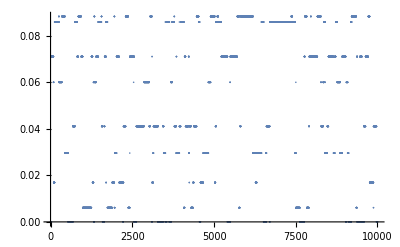

```mathematica
EDD//ListPlot
```

```mathematica
LL=62;
strconf=Table[0,{i,1,LL/2-3}];
strconf=Flatten[Prepend[strconf,{4,2,1}]];
prob=Product[Binomial[LL-Sum[strconf[[j]]t[i,j],{j,1,LL/2}],strconf[[i]]],{i,1,LL/2}]/(Binomial[LL,LL/2]-Binomial[LL,LL/2-1])
```

7.21939×10^-7

```mathematica
4/(1(2)(3))+2/(2(3)(4))+1/(3(4)(5.))
```

0.766667

```mathematica
100/60.
```

1.66667

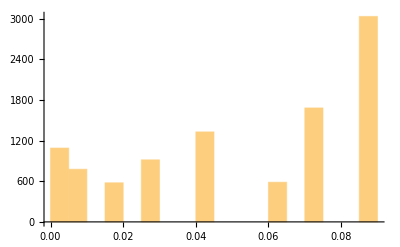

```mathematica
Histogram[EDD]
```

```mathematica
Export["/scratch/valba/GGE/test.dat",EDD]
```

/scratch/valba/GGE/test.dat

```mathematica
EDD
```

{1.91844,1.91844,1.91844,1.91844,2.68098,1.86457,0.681494,0.681494,0.391227,1.98991,1.66206,1.66206,1.66206,3.41041,3.41041,4.83748,0.397973,0.397973,0.397973,2.69776,1.02752,0.33687,1.01941,1.01941,1.00564,1.00564,1.00564,1.00564,1.96576,0.0440268,0.683426,1.88732,2.0616,1.05261,1.02752,0.85353,1.71801,0.650421,0.650421,2.11932,2.28611,2.41024,1.38333,2.66421,2.66421,1.38734,1.38734,0.790737,0.999266,2.00886,1.41419,0.1215,0.962615,0.962615,1.00788,3.18892,3.32197,0.831689,1.27694,0.253429,1.75373,0.793793,2.40119,3.55839,3.55839,3.55839,3.55839,0.635822,0.635822,2.8441,2.8441,2.85388,2.06551,0.962615,3.33517,2.5417,0.427812,0.397973,0.963239,1.98991,0.83687,1.75321,1.74566,1.61069,1.07909,1.94693,2.85388,2.85388,3.41168,1.089,1.63706,2.8441,0.249463,0.10548,2.42097,0.219212,0.681494,0.883217,1.55486,1.13197,1.13197,3.78574,0.253429,0.253429,2.32441,1.88732,1.55486,0.213849,0.213849,0.42427,1.26032,1.26032,1.20541,3.75153,2.30719,2.8629,2.8629,0.535075,1.88732,0.85138,0.85138,0.324125,0.324125,0.324125,0.324125,0.324125,1.27726,2.90967,2.03717,0.149136,1.75586,1.75586,2.97643,4.49766,1.6123,1.08796,0.535075,4.62832,0.85138,2.06551,4.71191,1.80464,1.63706,1.13197,1.13197,1.2051,1.2051,3.77796,0.346144,2.46893,4.38255,4.01283,0.011487,1.83875,0.11374,1.85706,1.10136,0.600079,0.600079,0.600079,3.62013,3.62013,3.62013,2.00886,2.11932,0.0908381,2.0616,0.0637594,1.089,1.46108,2.56866,1.40562,2.18391,2.09052,4.33225,2.24739,4.7812,0.516086,0.391227,0.391227,1.32728,1.32728,4.06633,0.85138,0.33687,2.12307,0.286593,3.75153,1.83875,0.717612,2.03478,3.02425,1.66939,3.84659,3.84659,3.84659,4.2946,1.66206,1.66206,0.715138,3.32312,1.03381,1.03381,1.57453,0.486494,1.13037,1.00883,4.03112,4.03112,4.33225,1.08796,0.0637594,0.0637594,2.5417,2.5417,2.5417,0.149136,2.03478,0.425877,0.425877,0.793793,2.03478,1.91656,3.40596,0.0637594,3.62235,1.74974,1.74974,1.10136,1.10136,1.23162,1.69538,0.65522,0.65522,3.38878,0.157881,0.426249,4.2946,1.22065,2.07326,1.81249,1.81249,4.49766,0.426249,0.426249,0.426249,1.91844,1.91844,2.27722,4.2946,0.723841,2.30719,0.586559,1.94883,1.73162,2.34323,0.671455,0.818116,5.40624,3.34799,3.97174,2.67651,1.49784,1.76016,1.2051,0.262866,0.262866,1.02752,1.53251,2.07326,0.717612,0.45791,0.628587,2.34307,1.08796,1.08796,1.35957,0.0182036,1.73162,0.85138,5.61426,1.32728,1.32728,3.48861,2.67651,0.681494,0.681494,0.681494,4.37595,2.91024,4.47428,0.83687,4.47428,0.151086,1.86457,2.28112,3.12726,0.260547,0.260547,0.793793,0.793793,0.580258,2.42097,2.42097,4.62832,2.07326,2.68098,2.68098,1.34887,1.36919,0.831689,0.370709,0.370709,0.831689,2.34323,1.02752,1.02752,1.02752,0.848221,0.848221,0.652755,1.20279,3.33517,3.33517,0.149136,0.149136,3.20502,0.516086,0.516086,0.516086,3.684,0.795662,2.87215,2.12307,0.782658,3.19683,0.187062,4.62832,0.0447436,1.23162,0.157881,1.53318,0.0626286,2.09052,1.13197,3.28088,3.34799,0.224262,0.224262,0.224262,0.224262,0.224262,1.79433,2.19713,0.249463,0.249463,0.249463,1.52084,1.35957,2.48263,2.48263,1.66627,1.66627,1.66627,1.66627,0.516086,0.516086,2.69776,3.55672,3.23918,1.52084,0.681494,0.157881,1.53251,3.97174,2.40762,2.40762,1.40629,1.04045,1.04045,1.04045,3.59653,1.23103,1.53251,1.83875,3.34799,0.238768,0.238768,0.238768,0.144357,1.88732,0.45791,4.03112,1.04045,1.04045,2.03478,3.6053,3.6053,2.97643,1.53251,1.53251,2.87215,3.28088,3.28088,1.6123,2.48263,2.12307,2.41024,2.84617,1.53251,0.00620085,0.00620085,0.353175,1.80464,2.6947,2.6947,2.6947,1.17566,1.17566,1.17566,0.963239,3.78574,1.05261,1.05261,1.05261,0.45791,1.2051,0.586559,2.84617,3.02425,0.831689,0.324125,2.17521,1.32728,1.32728,0.011487,0.011487,4.2946,1.51879,2.33443,2.24863,0.33687,2.89726,4.7812,1.19885,1.19885,3.33517,3.33517,0.819858,1.48196,4.62832,2.99072,0.650421,4.2946,0.260547,1.02752,3.02888,3.02888,4.62832,1.95495,1.17566,1.17566,0.187062,0.187062,1.22065,4.2946,4.2946,4.2946,0.445218,0.0440268,1.12042,1.17566,1.17566,0.723841,0.723841,3.13806,0.717612,3.62235,0.445218,1.88732,0.890597,0.684659,0.397973,0.85353,4.47428,0.83687,0.65522,0.65522,2.17521,1.089,3.02425,3.02425,0.426249,4.62832,1.79433,1.79433,1.79433,1.79433,1.46915,0.249463,1.12042,1.63706,1.65995,2.0616,2.0616,2.66421,2.66421,1.36633,1.02752,1.02752,0.635822,1.72124,0.286319,1.65995,0.0626286,0.0626286,0.85353,4.03579,2.48263,2.48263,2.48263,2.1709,2.16367,2.40119,2.11932,4.33225,1.23162,2.98688,0.187062,5.61426,1.35957,1.35957,0.469935,0.469935,1.04045,1.04045,1.65995,1.04045,0.0182036,0.0182036,0.0182036,0.0182036,0.28709,1.36633,1.73162,1.20279,1.20279,1.20279,1.20279,0.151086,2.06551,2.32266,2.32266,2.45855,0.516086,2.87215,2.87215,1.089,3.78574,3.11341,3.11341,0.462305,0.462305,0.462305,0.462305,5.86841,0.715138,0.715138,0.151086,0.0182036,0.324125,1.2051,1.12842,1.12842,2.14645,2.14645,2.68098,4.49766,0.28709,1.36919,3.55672,3.55672,3.55672,1.22065,0.286319,2.8629,2.38735,1.02752,2.09052,2.09052,2.42097,1.74566,1.2051,1.2051,0.652755,1.73162,1.73162,1.73162,1.00883,4.03112,4.03112,1.00883,3.62028,3.62028,3.62028,2.7774,1.23103,6.22426,0.31486,3.05049,4.62832,4.62832,0.83687,0.83687,1.66627,2.84617,1.089,1.089,1.66206,2.11923,1.86457,0.0694981,0.0694981,1.27045,0.891706,2.44447,0.891706,1.66939,1.66939,0.437244,3.01015,2.19713,2.19713,0.0440268,0.0440268,0.0440268,0.0440268,0.0440268,0.0440268,3.55672,0.486494,1.38734,3.13806,4.7812,0.0182036,4.49766,1.94693,1.07259,1.07259,0.83687,1.51879,1.51879,1.74566,1.74566,1.48196,1.51879,1.01867,1.7759,3.61709,2.33443,2.90967,0.85138,0.85138,2.99072,2.99072,0.0626286,0.0626286,0.0626286,0.0626286,2.5417,2.44312,2.03717,1.36919,0.0182036,1.40562,1.46103,0.304932,1.19885,0.260547,1.35107,1.35107,1.65995,0.249463,2.87215,1.69538,2.11956,3.77796,3.77796,0.848221,2.24863,2.73212,0.699813,2.24739,3.04984,3.04984,3.04984,1.34887,2.11956,1.91844,3.59653,0.144357,1.79433,0.238768,1.07909,0.11374,0.782658,0.782658,2.12797,3.78574,3.78574,3.78574,0.437244,0.671455,0.671455,0.503537,0.503537,2.33443,2.03478,3.62235,2.7774,2.32441,1.53318,1.94693,2.11956,1.36633,1.63706,1.74566,1.41419,1.13197,1.20279,3.78574,3.78574,3.78574,2.45855,2.45855,1.71801,1.71801,1.01941,1.13197,0.83687,2.30947,1.46915,3.13806,1.94693,1.94693,1.94693,0.437244,2.44312,0.370709,0.370709,2.40119,1.94693,1.38333,1.49618,1.49618,1.49618,0.224262,1.64664,0.00620085,0.427812,5.40624,4.06633,0.795662,0.795662,3.41041,2.28611,0.684659,0.684659,1.52084,2.51385,0.681494,3.12726,0.0626286,1.10136,1.48196,0.331751,2.85388,1.2051,4.2946,1.07909,1.00564,0.324125,0.324125,1.26032,1.53251,0.42427,3.62013,0.717612,0.717612,0.717612,2.69776,1.83875,0.286319,0.286319,1.08796,5.40624,5.13456,1.66939,2.12307,0.671455,0.671455,3.33517,3.33517,2.45515,0.470288,2.00886,1.36633,3.62235,3.62235,0.671455,3.04984,3.04984,1.18234,3.62013,1.2051,1.27694,1.27694,3.32312,4.7812,2.30719,0.42427,2.12307,2.1709,2.1709,2.1709,1.88732,2.03717,1.49784,2.8629,3.32197,3.32197,3.61709,2.41024,2.41024,2.41024,2.1709,2.1709,2.1709,2.45855,2.6947,2.6947,0.963239,1.80464,1.80464,0.883217,1.66939,2.83135,1.52084,1.39271,1.39271,1.39271,3.62235,3.62235,1.95495,2.33443,1.42771,1.42771,2.03478,0.891706,0.901105,3.62013,3.62013,2.67651,1.26032,0.681494,2.67651,0.414928,0.414928,0.414928,1.83875,0.717612,0.238768,1.12842,1.65475,0.614804,0.614804,0.614804,0.635822,2.11956,2.11956,3.41168,3.41168,3.78574,3.78574,1.94693,1.94693,3.02425,2.16367,3.59653,1.81249,2.14645,0.470288,1.48196,1.88732,0.963239,4.37595,3.38878,0.262866,2.19713,1.72926,0.652755,1.55486,0.901105,2.46893,0.370709,0.370709,3.77796,3.01015,3.01015,3.01015,2.09035,2.09035,2.09035,1.00564,1.00564,1.93184,2.03717,2.6947,2.69776,0.469935,1.42771,0.23687,3.77796,2.8441,3.75153,1.91844,1.07259,2.48263,2.26805,1.04361,1.04361,1.04361,4.49766,4.49766,4.49766,3.0187,3.0187,3.0187,0.516086,1.27694,0.462305,1.53318,2.12797,1.00788,1.00788,3.62235,3.62235,2.24863,1.49998,1.49998,0.203904,0.203904,1.66939,2.09035,2.09035,0.586559,2.30719,1.73162,0.667855,0.667855,0.667855,0.883217,0.818116,0.253429,0.635822,1.07909,1.40904,1.40904,1.40904,1.40904,0.723841,2.11956,0.0440268,1.00883,0.458813,0.458813,0.249463,2.352,3.02888,0.469935,1.22065,1.22065,2.84617,0.238768,1.94883,2.11956,2.12797,0.219212,2.55425,2.55425,2.55425,2.44312,2.91024,1.2051,3.05049,3.32197,2.30413,3.02425,3.02425,3.02425}

```mathematica
3.765611086679564 +4.6457
```

8.41131

```mathematica
Length[EDD]
```

1000